```mathematica
Clear["Global`*"]
```

# Average Countersunk Diameter

## Motivation

The average fastener diameter is calculated using this expression D + H^2(tan(50))/t which just means you take the area under the piecewise linear function and you divide throughout by the thickness t. However, this is not perfect since the real volume is that of a volume of revolution for the fastener head. The purpose of this notebook is to calculate a more precise version of the average diameter, ignoring any recession due to the indentation of the countersunk head.

-Graphics-

## Fastener Head Volume

The cross section of a countersunk fastener can be modelled as a piecewise linear function.

The side of the fastener head can be modelled using a straight line (y = mx + c), the volume of revolution is given by π∫_(H-t)^t y^2 ⅆx = π∫_(H-t)^t (mx+c)^2 ⅆx

```mathematica
FullSimplify[Pi * Integrate[(m*x+c)^2,{x,t-H,t}]]
```

(π ((c+m t)^3-(c+m (-H+t))^3))/(3 m)

For a countersunk fastener, the gradient  is tan(50), the y-intercept is the radius - m(t-H) since at the start of the countersunk head (t - H), the radius is the shank radius.

(π ((c+m t)^3-(c+m (-H+t))^3))/(3 m)

This is what I got by integrating by hand . We add the volume of the bottom shank which is a cylinder with height t - H and shank diameter d. Then the following expression gives the volume of the bottom half of the shank and the top half of the fastener head.

```mathematica
FullSimplify[(Pi*((m^2/3) (t^3-(t-H)^3)+m*c*(t^2-(t-H)^2)+c^2*(H))+ (Pi/4)*d^2*(t-H))]
```

1/4 d^2 π (-H+t)+1/3 H π (3 c^2-3 c m (H-2 t)+m^2 (H^2-3 H t+3 t^2))

This is what Mathematica obtained through integrating via volume of revolution.

```mathematica
FullSimplify[((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H)))]
```

1/4 d^2 π (-H+t)+(π ((c+m t)^3-(c+m (-H+t))^3))/(3 m)

## Average Diameter through an equivalence of volumes

To obtain the average diameter, take the sum of these two volumes and compare them to an equivalent volume cylinder with height t. This means we must multiply the expression by 4/πt and take the square root of the expression.

```mathematica
FullSimplify[((Pi*((m^2/3)*(t^3-(t-H)^3)+m*c*(t^2-(t-H)^2)+c^2*(H))+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)]
```

(√((12 c^2 H-12 c H m (H-2 t)+3 d^2 (-H+t)+4 H m^2 (H^2-3 H t+3 t^2))/t))/(√3)

```mathematica
FullSimplify[((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)]
```

(√((3 d^2 (-H+t)+(4 ((c+m t)^3-(c+m (-H+t))^3))/m)/t))/(√3)

Define the variables m which is the gradient, and c which is the y-intercept.

```mathematica
m = Tan[50 Degree]
```

Cot[40 °]

```mathematica
c = (d/2)- Tan[50 Degree]*(t-H)
```

d/2-(-H+t) Cot[40 °]

We check that my hand calculation is equivalent to Mathematica’s solution to the problem.

```mathematica
FullSimplify[((Pi*((m^2/3)*(t^3-(t-H)^3)+m*c*(t^2-(t-H)^2)+c^2*(H))+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)]
```

√(d^2+(2 d H^2 Cot[40 °])/t+(4 H^3 Cot[40 °]^2)/(3 t))

```mathematica
FullSimplify[((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)]
```

√(d^2+(2 d H^2 Cot[40 °])/t+(4 H^3 Cot[40 °]^2)/(3 t))

For convenience, we derive the same formula with the assumption of the height being H + T, where T is the positive unilateral tolerance.

```mathematica
FullSimplify[((Pi * Integrate[(m*x+c)^2,{x,t-H-T,t}]+ (Pi/4)*d^2*(t-H-T))/((Pi/4)*t))^(1/2)]
```

√(d^2+(2 d (H-T) (H+T) Cot[40 °])/t+(4 (H^3+T^3) Cot[40 °]^2)/(3 t))

```mathematica
FullSimplify[((Pi * Integrate[(m*x+c)^2,{x,t-(H+T),t}]+ (Pi/4)*d^2*(t-(H+T)))/((Pi/4)*t))^(1/2)]
```

√(d^2+(2 d (H-T) (H+T) Cot[40 °])/t+(4 (H^3+T^3) Cot[40 °]^2)/(3 t))

This expression gives the exact average diameter of a countersunk fastener. Note that cotangent 40 degrees is tangent 50 degrees. This is an exact formula for the head of a countersunk fastener. Typical calculations assumes that the volume of the countersunk fastener is equivalent by extrusion. This gives an expression D + H^2(tan(50))/t which just means you take the area under the piecewise linear function and you divide throughout by the thickness t.

Take the HL11 standard, assume the fastener head is 1.194 mm. Take the thickness of the sheet to be 3 mm.

```mathematica
t = 3; H= 1.194;
```

We plot the graph of the average fastener diameter against the nominal fastener diameter.

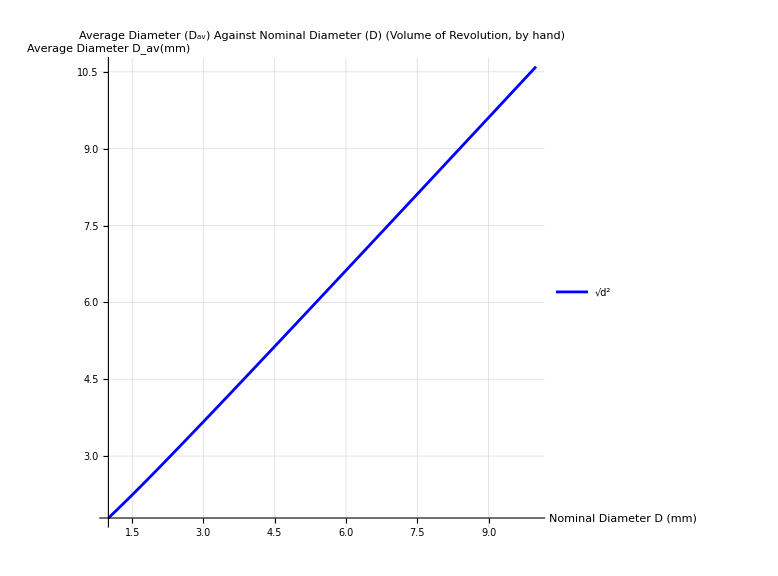

```mathematica
Plot[(((Pi*((m^2/3)*(t^3-(t-H)^3)+m*c*(t^2-(t-H)^2)+c^2*(H))+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)),{d,1,10},
AxesLabel->{"Nominal Diameter D (mm)","Average Diameter D_av(mm)"},
PlotLabel->"Average Diameter (D_av) Against Nominal Diameter (D) (Volume of Revolution, by hand)",
PlotStyle->Blue,
PlotRange->All,
PlotLegends->{"√(d^2)"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
]
```

Here we used Mathematica to compute the integral directly and do the same plot.

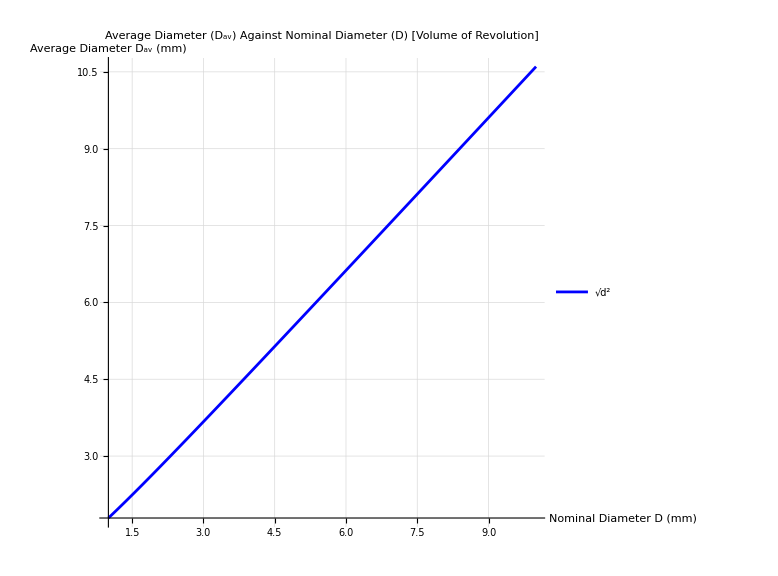

```mathematica
Plot[(((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)),{d,1,10},
AxesLabel->{"Nominal Diameter D (mm)","Average Diameter D_av (mm)"},
PlotLabel->"Average Diameter (D_av) Against Nominal Diameter (D) [Volume of Revolution]",
PlotStyle->Blue,
PlotRange->All,
PlotLegends->{"√(d^2)"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
]
```

Here we used the default approximation for the fastener average diameter.

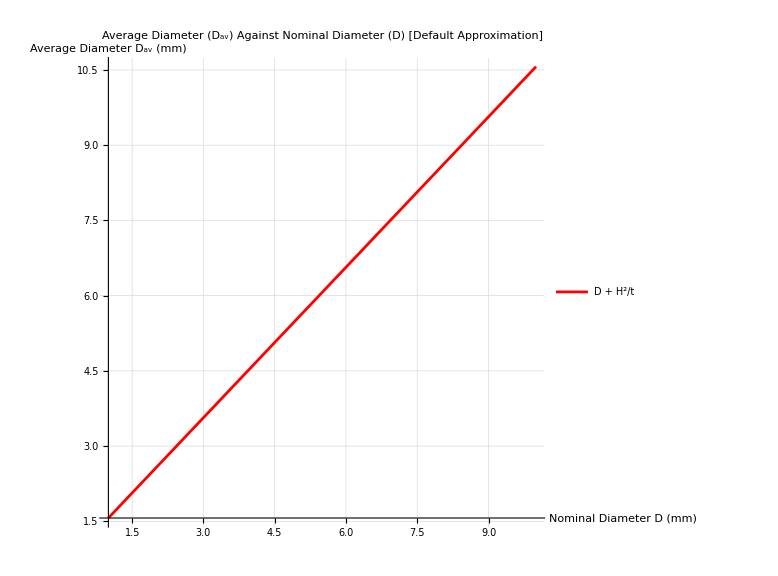

```mathematica
Plot[((d+(H^2*m/t))),{d,1,10},
AxesLabel->{"Nominal Diameter D (mm)","Average Diameter D_av (mm)"},
PlotLabel->"Average Diameter (D_av) Against Nominal Diameter (D) [Default Approximation]",
PlotStyle->Red,
PlotRange->All,
PlotLegends->{"D + H^2/t"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
]
```

We can put the two plots together to show the differences in the value of the average diameter given these two plots. Given our assumptions of the shank head height and the sheet thickness.

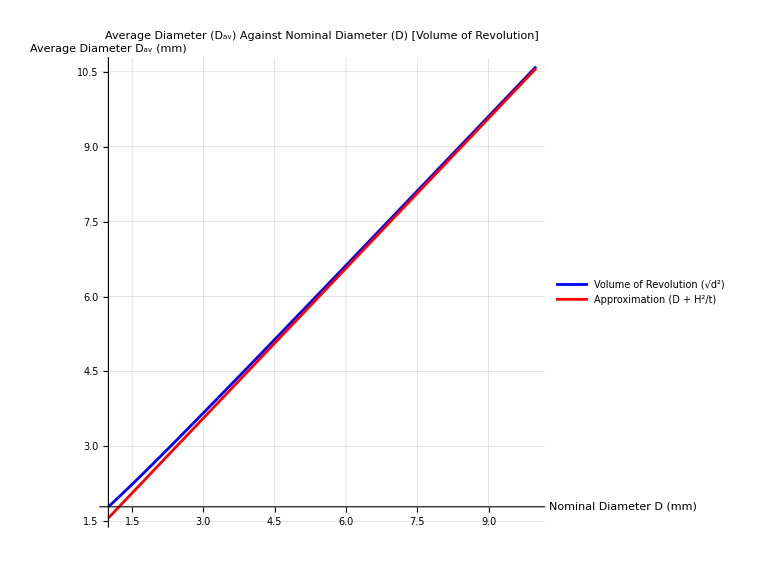

```mathematica
Plot1 = Plot[(((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)),{d,1,10},
AxesLabel->{"Nominal Diameter D (mm)","Average Diameter D_av (mm)"},
PlotLabel->"Average Diameter (D_av) Against Nominal Diameter (D) [Volume of Revolution]",
PlotStyle->Blue,
PlotRange->All,
PlotLegends->{"Volume of Revolution (√(d^2))"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
];
Plot2 = Plot[((d+(H^2*m/t))),{d,1,10},
AxesLabel->{"Nominal Diameter D (mm)","Average Diameter D_av (mm)"},
PlotLabel->"Average Diameter (D_av) Against Nominal Diameter (D) [Default Approximation]",
PlotStyle->Red,
PlotRange->All,
PlotLegends->{"Approximation (D + H^2/t)"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
];
Show[Plot1,Plot2]
```

We can plot the error in the approximation due from not assuming revolution to assuming that there is revolution.

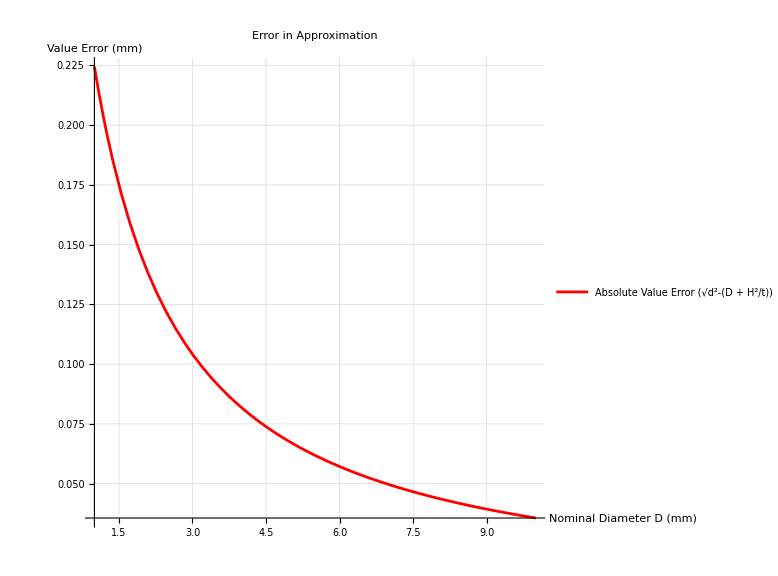

```mathematica
Plot[(((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2))-((d+(H^2*m/t))),{d,1,10},AxesLabel->{"Nominal Diameter D (mm)","Value Error (mm)"},
PlotLabel->"Error in Approximation",
PlotStyle->Red,
PlotRange->All,
PlotLegends->{"Absolute Value Error (√(d^2)-(D + H^2/t))"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
]
```

Similarly, calculate the percentage error in the approximation. For this given case, it is less than 5% at nominal diameters more than 2 mm.

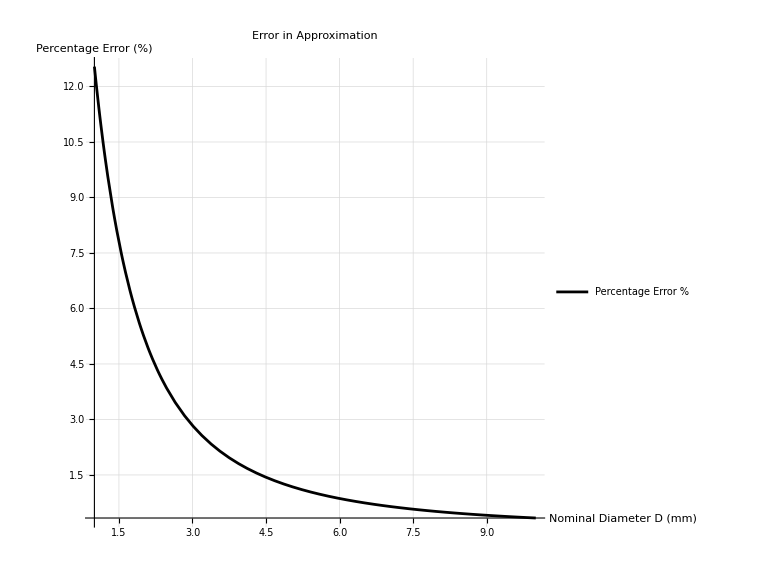

```mathematica
Plot[(((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2)-((d+(H^2*m/t))))/(((Pi * Integrate[(m*x+c)^2,{x,t-H,t}]+ (Pi/4)*d^2*(t-H))/((Pi/4)*t))^(1/2))*100,{d,1,10},AxesLabel->{"Nominal Diameter D (mm)","Percentage Error (%)"},
PlotLabel->"Error in Approximation",
PlotStyle->Black,
PlotRange->All,
PlotLegends->{"Percentage Error %"},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1 ,
ImageSize->Large
]
```